```mathematica
f[x_]= (x^2-1)/(x^2-4)
```

(-1+x^2)/(-4+x^2)

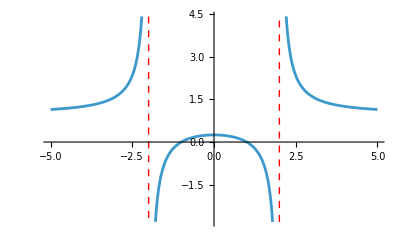

```mathematica
Plot[f[x], {x,-5,5}, ExclusionsStyle->{{Dashed, Red}}]
```

```mathematica
Solve[ (x^2-1)/(x^2-4),x]
```

Solve::naqs: (-1+x^2)/(-4+x^2) is not a quantified system of equations and inequalities.

```mathematica
Solve[f[x]== 0,x]
```

{{x→-1},{x→1}}

```mathematica
Solve[Denominator[f[x]]==0,x]
```

{{x→-2},{x→2}}

```mathematica
Solve[Denominator[f[x]]==0,x]
```

{{x→-2},{x→2}}

```mathematica
Limit[f[x], x->2, Direction->1]
```

-∞

```mathematica
Limit[f[x], x->∞]
```

1

```mathematica
D[f[x],x]
```

(2 x)/(-4+x^2)-(2 x (-1+x^2))/((-4+x^2)^2)

```mathematica
Solve[(2 x)/(-4+x^2)-(2 x (-1+x^2))/((-4+x^2)^2)==0,x]
```

Syntax::sntxb: Expression cannot begin with "[(2x)/(-4+x^2)-(2x(-1+x^2))/((-4+x^2)^2)]==0".

```mathematica
First[{{x->0}}]
```

{x→0}

```mathematica
g[x_]=(2 x)/(-4+x^2)-(2 x (-1+x^2))/((-4+x^2)^2)
```

(2 x)/(-4+x^2)-(2 x (-1+x^2))/((-4+x^2)^2)

```mathematica
Solve[Numerator[g[x]]==0,x]
```

{{x→0}}

```mathematica
D[f[x],{x,2}]
```

-(8 x^2)/((-4+x^2)^2)+2/(-4+x^2)+(-1+x^2) ((8 x^2)/((-4+x^2)^3)-2/((-4+x^2)^2))

```mathematica
Reduce[Out[113]>0,x]
```

x<-2||x>2

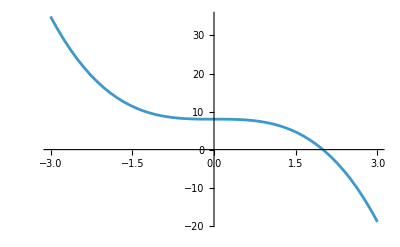

```mathematica
Plot[-x^3+8, {x,-3,3}]
```

```mathematica
Integrate[-x^3+8, {x,0,2}]
```

12

```mathematica
s[x_]= x^2-8
```

-8+x^2

```mathematica
z[x_]=-x^2+10
```

10-x^2

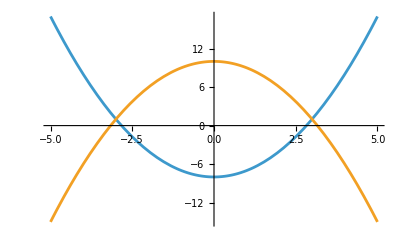

```mathematica
Plot[{s[x],z[x]},{x,-5,5}]
```

```mathematica
Solve[s[x]==z[x],x]
```

{{x→-3},{x→3}}

```mathematica
Integrate[z[x]-s[x], {x , -3,3 }]
```

72

```mathematica
Plot[{s[x],z[x]},{x,-5,5},Filling{1->{2}}]
```

Plot::nonopt: Options expected (instead of Filling {1→{2}}) beyond position 2 in Plot[{s[x],z[x]},{x,-5,5},Filling {1→{2}}]. An option must be a rule or a list of rules.

```mathematica
Plot[{s[x],z[x]},{x,-5,5},Filling ->s]
```

-Graphics-

```mathematica
NSolve[x^7-2x^6-x^5 - 2x^4 + 12x^2 - x + 1==0,x]
```

{{x→-1.37527},{x→-0.356206-1.47367 ⅈ},{x→-0.356206+1.47367 ⅈ},{x→0.040941-0.283889 ⅈ},{x→0.040941+0.283889 ⅈ},{x→1.59494},{x→2.41086}}

```mathematica
Solve[1+Re[-x+12 x^2-2 x^4-x^5-2 x^6+x^7],x]
```

```mathematica
Reduce[Abs[x-3]/(x+1)>√(3-2x),x, Reals]
```

-1<x<1||1<x≤3/2

```mathematica
Reduce[Conjugate[z]==z^2,z, Complexes]
```

z==0||z==1||z==-1/2-(ⅈ √3)/2||z==-1/2+(ⅈ √3)/2

```mathematica
Solve[(4a+3a)/(3a+10)==(3a-4)/(3a-10),a]
```

{{a→1/3 (11-√91)},{a→1/3 (11+√91)}}

```mathematica
Solve[{3==-2k+n, -1==6k+n},{k,n}]
```

{{k→-1/2,n→2}}

```mathematica
∑_(n=1)^k 16-2n
```

16 k-2 n

```mathematica
Sum[16-2n,{n,1,k}]
```

15 k-k^2

```mathematica
Solve[15k-k^2==36, k]
```

{{k→3},{k→12}}